# Bitcoin Price Movements

This notebook serves to analyze Bitcoin price movements on either a daily, weekly, or monthly basis .

```mathematica
(* Buttons to hide / show code *)
CloseAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];SetOptions[#,CellOpen->False]&/@cells;];

OpenAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];SetOptions[#,CellOpen->True]&/@cells;];

Row[{Button["Hide Code",SelectionEvaluate[CloseAllInputsCells[]]],Button["Show Code",SelectionEvaluate[OpenAllInputsCells[]]]}]
```

Hide CodeShow Code

```mathematica
(* Since Mathematica operates in a global environment, let's clear all that, so we're clean *)
Clear["Global`"];

(* The earliest date for data *)
origindate="Sep. 14, 2011";

(* Put these stats in the summary boxes placed within each plot *)
bstats[lst_]:=Return[<|
count->Length[lst]
,min->Min[lst]
,mean->Mean[lst]
,median-> Median[lst]
,max->Max[lst]
,std->StandardDeviation[lst]
|>//Dataset];

(* Time increment strings for selection *)
ly[str_]:=Switch[str,"Day","Daily","Week","Weekly","Month","Monthly","Year","Yearly"];

(* Default properties for generated plots *)
imagesize=1250;
labelstyle=Directive[14];
imagemargins=20;
plotbackground=Lighter[LightGray,0.75];
ticks2={#,ToString[Quantity[100 #,"Percent"],StandardForm]}&/@Range[-1,1,1/10];
```

```mathematica
(* Here we fetch the data, and normalize it from a Dataset to a plain list *)
btcDataFull = FinancialData["BTC/USD", origindate]//Normal;
(* How many days data have we got? *)
days = btcDataFull//Length;

(* How much of the list do we take for display? *)
takes=MapIndexed[
#1->Style[ToString[First[#2]]<> " yr",16]&
,Join[
Range[365,days,365]
,{days}
]
]//ReverseSort;
```

```mathematica
(* The real fun begins here *)
Manipulate[
(* insetscale places some of the inset stat boxes horizontally *)
insetscale={.07,.875};
intervally=ly[interval];
btcData=TimeSeriesAggregate[Take[btcDataFull,-since],interval,Last];

(* A B S O L U T E   C H A N G E S *)
absolutechanges = Table[Last[btcData[[n]]]-Last[btcData[[n-1]]],{n,2, Length@btcData}];
tsabsolutechanges= TimeSeries[Table[{First[btcData[[n]]],Last[btcData[[n]]]-Last[btcData[[n-1]]]},{n,2, Length@btcData}]];
dlpabsolute=DateListPlot[
tsabsolutechanges
,PlotLabel->Column[{"Absolute "<> intervally <> " Dollar Changes",ToString[tsabsolutechanges["Values"]//Length]<> " " <>interval <> "s"},Center]
,ImageSize->imagesize
,ImageMargins->20
,PlotRange->Full
,FrameTicks->All
, GridLines->Automatic
, Joined->False
,FrameLabel->{{HoldForm[US Dollars],None},{None,None}}
,LabelStyle->labelstyle
,ImageMargins->imagemargins
,Background->plotbackground
,Epilog->
Inset[
Framed[bstats[absolutechanges]]
,Scaled[insetscale]
,Background->White
]
];
rankabs=SortBy[tsabsolutechanges//Normal,Last];
worst=Take[rankabs,Min[100,Length[rankabs]]]//Dataset;
best=ReverseSortBy[Take[rankabs,Max[-100,-Length[rankabs]]],#[[2]]&]//Dataset;
worstandbest=Column[{
Style["Worst and Best",{20, Red}]
,Row[{worst,best}
,ImageSize->600
, Alignment->Center
]
}
,Alignment->Center
, Frame->True
];

(* R E L A T I V E   C H A N G E S *)
relativechanges = Table[
{
First[btcData[[n]]],(Last[btcData[[n]]]-Last[btcData[[n-1]]])/(Mean[{Last[btcData[[n]]],Last[btcData[[n-1]]]}])
}
,{n,2, Length@btcData}
];
tsrelativechanges = TimeSeries[relativechanges];
dlprelative=DateListPlot[tsrelativechanges
,PlotLabel->Column[{"Relative " <> intervally <> " Changes",ToString[Length[tsrelativechanges["Values"]]]<> " " <> interval <> "s"},Center]
,PlotRange->All
,GridLines->{DateRange[{2011},{2030},"Year"],Range[-1,1,1/10]}
,Ticks->{Automatic,ticks2}
,FrameTicks->All
,Joined->False
,PlotMarkers->{Automatic,Scaled[0.005]}
,Filling->Axis
,FillingStyle->{Red, Green}
,Background->plotbackground
,ImageSize->imagesize
,LabelStyle-> labelstyle
,ImageMargins->imagemargins
,Epilog->
Inset[
Framed[bstats[tsrelativechanges["Values"]]]
,Scaled[insetscale]
,Background->White
]
];
positives=Select[tsrelativechanges["Values"],#>0& ];
negatives=Select[tsrelativechanges["Values"],#<0& ];
mhistpositive=Histogram[
positives
,25
,PlotLabel->Column[{intervally <> " Positive Price Movements",ToString[positives//Length]<> " of "<>ToString[Length[positives] +Length[ negatives]]<> " " <> interval <>"s"},Center]
,PlotRange->Full
,ImageSize->imagesize
,GridLines->Automatic
,Ticks->{ticks2, Automatic}
,FrameTicks->All
,ChartStyle->Green
,LabelStyle->labelstyle
,ImageMargins->imagemargins
,LabelingFunction->Above
,Background->plotbackground
,Epilog->Inset[
Framed[bstats[positives]]
,Scaled[{.50,.85}]
,Background->White
]
];
mhistnegative=Histogram[
{negatives}
,50
,PlotLabel->Column[{intervally <> " Negative Price Movements",ToString[Length[negatives]]<> " of "<>ToString[Length[positives] +Length[ negatives]]<>" " <> interval <> "s"},Center]
,PlotRange->Full
,ImageSize->imagesize
,GridLines->Automatic
,Ticks->{ticks2, Automatic}
,FrameTicks->All
,ChartStyle->Red
,LabelStyle->labelstyle
,LabelingFunction->Above
,ImageMargins->imagemargins
,LabelingFunction->Above
,Background->plotbackground
,Epilog->Inset[
Framed[bstats[negatives]]
,Scaled[{.50,.85}]
,Background->White
]
];
mhistcombined=Manipulate[
Histogram[{positives,negatives}, x
,PlotLabel->Column[{"Relative " <> intervally <> " Movements",ToString[Length[positives] +Length[ negatives]]<> " " <> interval <> "s"},Center]
,PlotRange->Full
,GridLines->{Range[-1,1,1/10],Automatic}
,Ticks->{ticks2, Automatic}
,FrameTicks->All
,ChartStyle->{Green, Red}
,ImageSize->imagesize
,ImageMargins->imagemargins
,LabelStyle->If[x>75,labelstyle,{labelstyle,Directive[If[x<50,12,8]]}]
,LabelingFunction->If[x>75,None,Above]
,Background->plotbackground
,Epilog->{
Inset[
Framed[bstats[Join[positives,negatives]]]
,Scaled[{.30,.90}]
,Background->White
]
,Inset[
Framed[bstats[negatives]]
,Scaled[{.10,.40}]
,Background->White
]
,Inset[
Framed[bstats[positives]]
,Scaled[{.90,.40}]
,Background->White
]
}
]
,{{x,50,Style["Bins: ",{15}]},Range[10,200,10]}
];
Column[{
Style["Absolute "<> intervally <> " Movements","Section"]
,dlpabsolute
,worstandbest
,Spacer[10]
,Style["Relative "<>intervally<>" Movements","Section"]
,dlprelative
,mhistpositive
,mhistnegative
,mhistcombined
}
],
{
{interval,"Day"}
,#->Style[#,16]&/@{"Day", "Week","Month"}
}
, {
{since,days}
, takes
}
]
```

## Starting here to quantify price volatility (not ready for prime time yet)

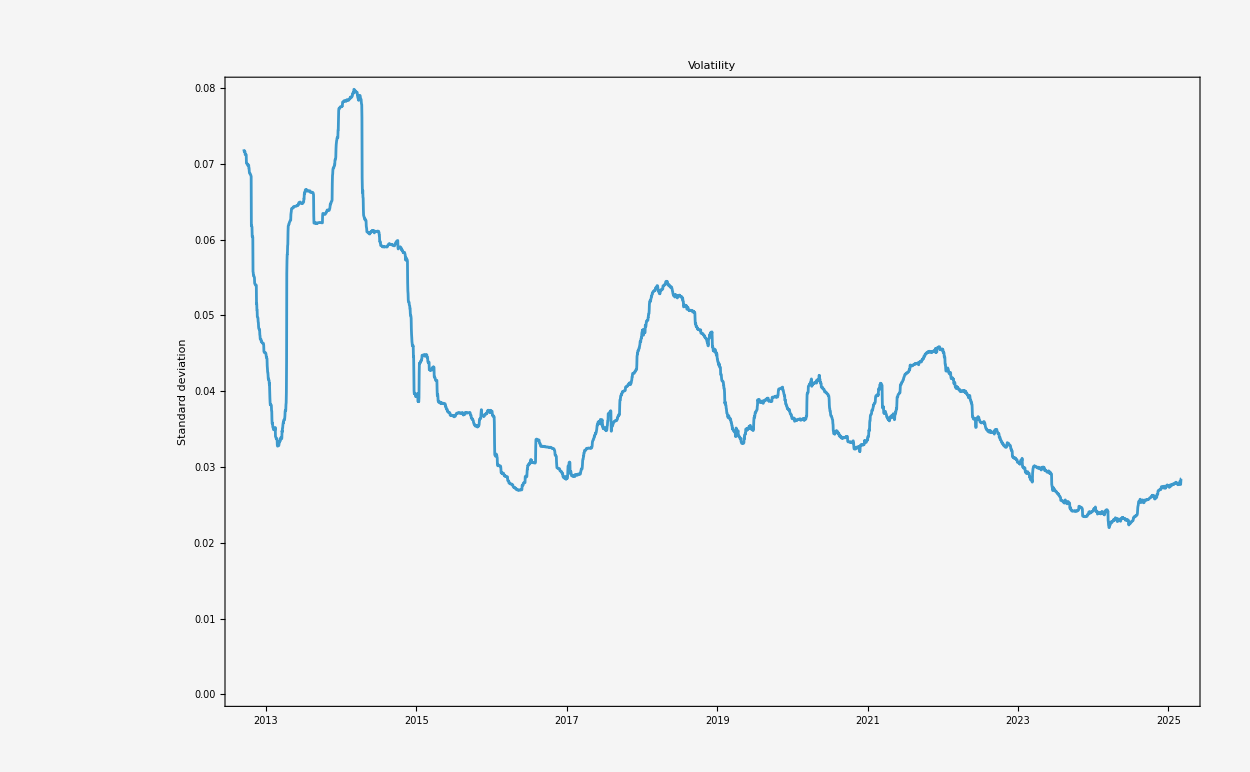

```mathematica
relativechangesall = Table[
{
First[btcDataFull[[n]]]
,(Last[btcDataFull[[n]]]-Last[btcDataFull[[n-1]]])/Mean[{Last[btcDataFull[[n]]],Last[btcDataFull[[n-1]]]}]
}
,{n,2, Length@btcDataFull}
];
tsrelativechangesall = TimeSeries[relativechangesall];
annualvolatility=MovingMap[StandardDeviation,tsrelativechangesall,Quantity[12,"Months"]];
DateListPlot[
annualvolatility
,PlotLabel->"Volatility"
,ImageSize->imagesize
,ImageMargins->20
,ImageMargins->imagemargins
,Background->plotbackground
,PlotRange->Full
,FrameTicks->All
,GridLines->{Automatic,Range[0,0.2,0.01]}
,FrameLabel->{{HoldForm[Standard deviation],None},{None,None}}
,LabelStyle->labelstyle
]
```